#### 7.5.1b

```mathematica
f[A_,B_,t_]:=A*Exp[-t]+2*B*Exp[2t]
```

```mathematica
g[A_,B_,t_]:=2*A*Exp[-t]+B*Exp[2t]
```

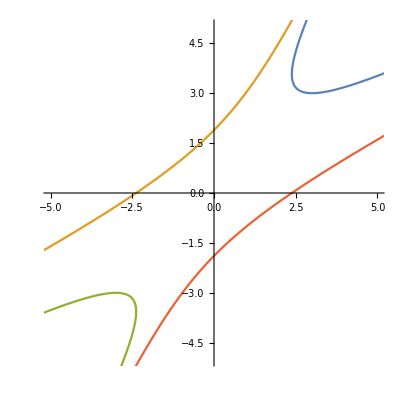
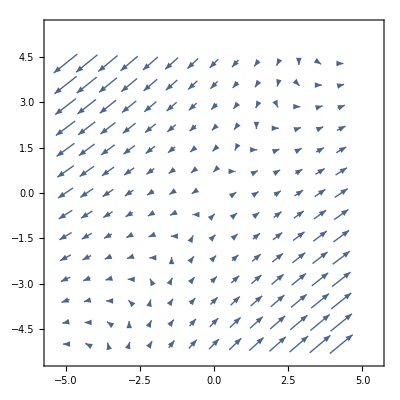

```mathematica
Overlay[{ParametricPlot[{{f[1,1,t], g[1,1,t]},{f[1,-1,t], g[1,-1,t]},{f[-1,-1,t], g[-1,-1,t]},{f[-1,1,t], g[-1,1,t]}},{t,-1,1}, PlotRange-> {{-5,5},{-5,5}}],VectorPlot[{3x-2y,2x-2y},{x,-5,5},{y,-5,5}]}]
```

#### 7.5.3b

```mathematica
h[a_,b_,t_]:=a*Exp[-t]+b Exp[t]
```

```mathematica
k[a_,b_,t_]:=3 a Exp[-t]+b Exp[t]
```

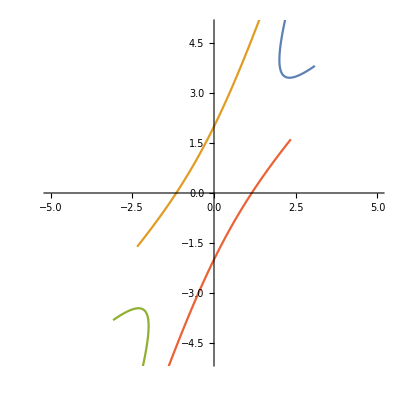
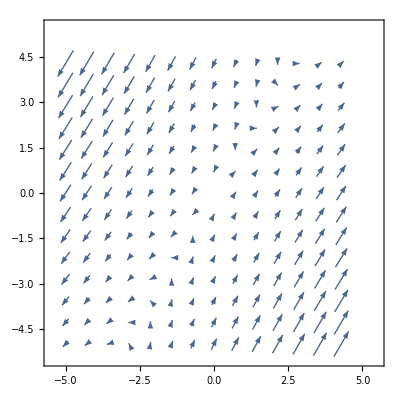

```mathematica
Overlay[{ParametricPlot[{{h[1,1,t], k[1,1,t]},{h[1,-1,t], k[1,-1,t]},{h[-1,-1,t], k[-1,-1,t]},{h[-1,1,t], k[-1,1,t]}},{t,-1,1}, PlotRange-> {{-5,5},{-5,5}}],VectorPlot[{2x-y,3x-2y},{x,-5,5},{y,-5,5}]}]
```